```mathematica
F[t_,x_]:=1/2-Sum[16*((4*m+2)*π)^(-2)*Exp[-((4*m+2)*π)^2*t]*Cos[(4*m+2)*π*x],{m,0,1000}]
```

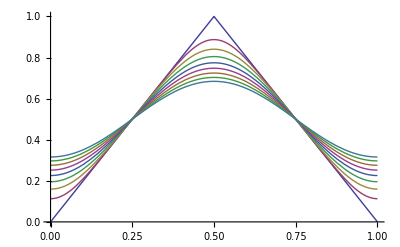

```mathematica
Plot[{F[0,x],F[0.0025,x],F[0.0050,x],F[0.0075,x],F[0.01,x],F[0.0125,x],F[0.0150,x],F[0.0175,x],F[0.02,x]},{x,0,1}]
```